## Time-dependent “Perturbations”

Consider a time-dependent perturbation V(t), added to a time-independent H^0, (the atom) with eigenstates k.  At t=0, the atom is in the state k=g.  We can expand the quantum state as a function of time as

ψ=c_g ⅇ^(-ⅈ E_g t/ℏ)g+∑_(k≠g) c_k ⅇ^(-ⅈ E_k t/ℏ)k

We first assume that the effect of the perturbation is small, so that |c_g|≈1 and c_k≪1.  The inner product kψ̇ is

ⅈ ℏ kψ̇=(ⅈ ℏ (ċ)_k+E_k c_k)ⅇ^(-ⅈ E_k t/ℏ)=k H^0 ψ+kV(t)ψ=E_k kψ+kVψ
ⅈ ℏ (ċ)_k=V_kg c_g ⅇ^(ⅈ (E_k-E_g)t/ℏ)+∑_(n≠k,g) V_kn c_n ⅇ^(ⅈ (E_k-E_n)t/ℏ)

The initial conditions are c_g(0)=1, c_k(0)=0.  For small V,  c_k∝V so the c_n terms can be neglected, giving

ⅈ ℏ (ċ)_k=V_kg ⅇ^(ⅈ (E_k-E_g)t/ℏ)c_g

whose solution is

ⅈ ℏ c_k=c_g(∫_0)^t ⅆt' ⅇ^(ⅈ ω_kg t')V_kg(t')

We have introduced the Bohr frequency ω_kg:   ℏ ω_kg=E_k-E_g.  If we presume V_kg(t')=0 for t'<0 and t'>t (the future) then this becomes a Fourier transform:

ⅈ ℏ c_k=∫_(-∞)^∞ ⅆt' ⅇ^(ⅈ  ω_kg t')V_(k g)(t')=(Ṽ)_(k g)(ω_(k g))

### Example: V=const

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

(Ṽ)_kg(ω_kg)=V_kg∫_0^t ⅆt' ⅇ^(ⅈ  ω_kg t')

```mathematica
Subscript[c, k]=Integrate[-ⅈ/ℏ Subscript[V, kg] ⅇ^(ⅈ Subscript[ω, kg] tp),{tp,0,t}];Subscript[c, k] SuperStar[Subscript[c, k]]//ExpToTrig//Simplify
```

(4 Sin[(t ω_kg)/2]^2 V_kg^2)/(ℏ^2 ω_kg^2)

For small t, this becomes

```mathematica
Series[(4 Sin[(t Subscript[ω, kg])/2]^2 Subscript[V, kg]^2)/(ℏ^2 Subscript[ω, kg]^2),{t,0,2}]//Normal
```

(t^2 V_kg^2)/ℏ^2

which says that perturbation theory will hold if V_kg t≪ℏ.  The theory will hold for all t if V_kg ω_kg^-1≪ℏ/2.    

Often V is applied for a fixed time t, and our formula then tells the probability of finding various states:

P_k=(4 Sin[(t ω_kg)/2]^2 V_kg^2)/(ℏ^2 ω_kg^2)=V_kg^2/ℏ^2 t^2 Sinc^2[(t ω_kg)/2]=P_max Sinc^2[(t ω_kg)/2]

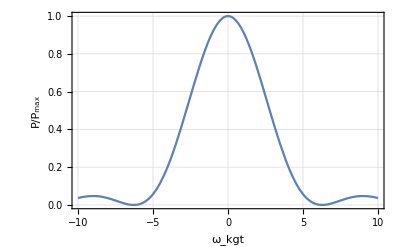

```mathematica
ThadPlot[Sinc[u/2]^2,{u,-10,10},PlotRange->All,{"ω_kgt","P/P_max"}]
```

If there are many states whose energies fall under this peak, and who have approximately the same matrix elements V_kg, the probability of population transfer to all states k≠ g is

P_tot=∑_k P_max Sinc^2[(t ω_kg)/2]=P_max∫_(-∞)^∞ ⅆN/(ⅆ E)ⅆE  Sinc^2[(t E)/(2ℏ)]=P_max ⅆN/(ⅆ E)∫_(-∞)^∞ ⅆE  Sinc^2[(t E)/(2ℏ)] 
=P_max ⅆN/(ⅆ E)(2 π ℏ)/t=V_kg^2/ℏ^2 t^2 ⅆN/(ⅆ E)(2 π ℏ)/t=(2 π)/ℏ V_kg^2 ⅆN/(ⅆ E)t

```mathematica
Integrate[Sinc[(t e)/(2ℏ)]^2,{e,-∞,∞},Assumptions->t/ℏ>0]
```

(2 π ℏ)/t

This is Fermi’s famous “Golden Rule”, which says that the rate of transfer to all states g is

∑_k R_kg=(2 π)/ℏ V_kg^2 ⅆN/(ⅆ E)

Notice that for a single state, the population transfer probability is proportional to t^2 at small t, but for many states the excitation probability is proportional to just t^1.

### Example 2: V=𝒱 cos[ω t]

(Ṽ)_kg(ω_eg)=∫_(-∞)^∞ ⅆt' 𝒱_kg cos[ω t']ⅇ^(ⅈ  ω_kg t')=1/2((𝒱̃)_kg(ω+ω_kg)+(𝒱̃)_kg(ω-ω_kg))

According to our previous discussion, we expect that if ω t>>1 the population will efficiently transfer only if ω≈|ω_kg|.  Assume the most common case ω_kg>0. Then, defining Δ_kg=,

(Ṽ)_kg(ω_eg)≈1/2(𝒱̃)_kg(ω-ω_kg)→ P_k=1/2 𝒱_kg^2/ℏ^2 t^2 Sinc^2[(t (ω-ω_kg))/2]

The probability of transfer maximizes when ω-ω_kg=0, or

ℏ ω=E_k-E_g,

which we recognize as the Bohr condition.  Viewed as  a spectroscopy experiment, the effective linewidth of the transition is approximately

Δω~1/(2π t)

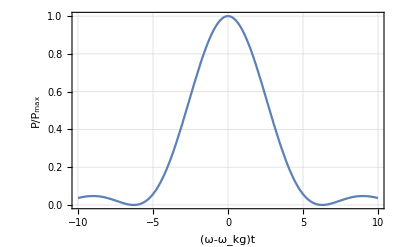

```mathematica
ThadPlot[Sinc[u/2]^2,{u,-10,10},PlotRange->All,{"(ω-ω_kg)t","P/P_max"}]
```

### Example 3: 2-level system: Rabi flopping

Suppose that ω≈ω_kg for a particular pair of levels, but for none other.  Then we know perturbation theory will break down for those 2 levels, but none other.  We return to the Schrodinger equation, but now assume only those two levels.  It will be convenient to make a slightly different assumption about the time dependencies: ψ≈ⅇ^(-ⅈ E_g t/ℏ)(a_g g+a_k ⅇ^(-ⅈ ω t)k).  This corresponds to a_g=c_g, a_k=c_k ⅇ^(-ⅈ(ℏ ω-E_k+E_g)t/ℏ).  We get

ⅈ ℏ (ȧ)_k+ℏω a_k=E_k a_k+𝒱_kg cos[ω t]ⅇ^(ⅈ ω t)a_g≈E_k a_k+𝒱_kg/2 a_g
ⅈ ℏ (ȧ)_g=𝒱_gk cos[ω t]ⅇ^(-ⅈ ω t)a_k≈𝒱_gk/2 a_k

We now understand that we can ignore terms oscillating at 2ω compared to those oscillating at zero frequency. We can write this as

ⅈ ℏ ⅆ_t(a_k
a_g)=(E_k-ℏ ω | 𝒱_kg/2
𝒱_gk/2 | 0)(a_k
a_g)

We have managed to transform our time-dependent Hamiltonian to a time-independent one, with the energy of state k shifted down by ℏ ω.  We can now apply the Schrodinger |□⟩ recipe:

```mathematica
psi=MatrixExp[-ⅈ {{-ℏ Δ, 𝒱/2}, {𝒱/2, 0}} t/ℏ].{0,1}//FullSimplify
```

{-(ⅈ ⅇ^((ⅈ t Δ)/2) 𝒱 Sin[(t √(𝒱^2+Δ^2 ℏ^2))/(2 ℏ)])/(√(𝒱^2+Δ^2 ℏ^2)),ⅇ^((ⅈ t Δ)/2) (Cos[(t √(𝒱^2+Δ^2 ℏ^2))/(2 ℏ)]-(ⅈ Δ ℏ Sin[(t √(𝒱^2+Δ^2 ℏ^2))/(2 ℏ)])/(√(𝒱^2+Δ^2 ℏ^2)))}

```mathematica
pkg=psi⟦1⟧ SuperStar[psi⟦1⟧]//Simplify
```

(𝒱^2 Sin[(t √(𝒱^2+Δ^2 ℏ^2))/(2 ℏ)]^2)/(𝒱^2+Δ^2 ℏ^2)

The populations oscillate back and forth in time at the “generalized Rabi frequency” √((𝒱/ℏ)^2+Δ^2).

```mathematica
$Assumptions={𝒱>0};
```

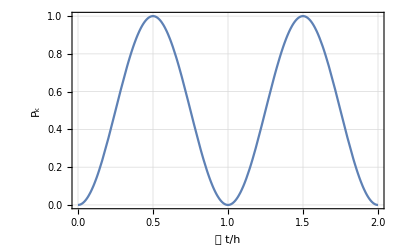

```mathematica
ThadPlot[pkg/.{Δ->0 ,t->u (2π ℏ)/𝒱}//Simplify,{u,0,2},PlotRange->All,{"𝒱t/h","P_k"}]
```

Viewed spectroscopically, assuming 𝒱 t=π ℏ:

```mathematica
(pkg/.𝒱->(π ℏ)/t//Simplify//PowerExpand)/.Sin[a_]->a Sinc[a]
```

1/4 π^2 Sinc[1/2 √(π^2+t^2 Δ^2)]^2

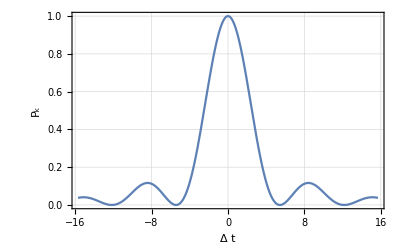

```mathematica
ThadPlot[%/.{Δ->u/t}//Simplify//PowerExpand,{u,-5π,5π},PlotRange->All,{"Δ t","P_k"}]
```

### Rabi flopping for arbitrary unitary operations

For quantum information applications, it is necessary to be able to make all possible unitary transformations of the single-particle qubits.  The Rabi Hamiltonian H_R[Δ,𝒱]=(-ℏ Δ | 𝒱/2
𝒱/2 | 0) provides a means for doing so.  A general unitary matrix for a 2-level system is

```mathematica
U(θ,ϕ)=({{Cos[θ/2], -ⅈ ⅇ^(ⅈ ϕ)Sin[θ/2]}, {-ⅈ ⅇ^(-ⅈ ϕ)Sin[θ/2], Cos[θ/2]}})
```

We will see how Rabi flopping can be used to produce U(θ,ϕ).

First, note that H_(R[)[Δ,0] produces rotations about the z-axis:

```mathematica
s=angmom[1/2];Subscript[H, R][Δ_,𝒱_]:=({{-ℏ Δ, 𝒱/2}, {𝒱/2, 0}});
MatrixExp[-ⅈ Subscript[H, R][Δ,0] t/ℏ]==ⅇ^(-(ⅈ α)/2)MatrixExp[-ⅈ s⟦3⟧ α]
```

{{ⅇ^(ⅈ t Δ),0},{0,1}}=={{ⅇ^(-ⅈ α),0},{0,1}}

and that H_(R[)[0,𝒱] produces rotations about the x-axis:

```mathematica
(MatrixExp[-ⅈ Subscript[H, R][0,𝒱] t/ℏ]== MatrixExp[-ⅈ s⟦1⟧ (t 𝒱)/ℏ])
```

True

Now consider a rotation about the x-axis sandwiched between two z-axis rotations

```mathematica
MatrixExp[-ⅈ s⟦3⟧ (-ϕ)].MatrixExp[-ⅈ s⟦1⟧ θ].MatrixExp[-ⅈ s⟦3⟧ (ϕ)]//Simplify//MF
```

(Cos[θ/2] | -ⅈ ⅇ^(ⅈ ϕ) Sin[θ/2]
-ⅈ ⅇ^(-ⅈ ϕ) Sin[θ/2] | Cos[θ/2])

Using Rabi rotations, this is

```mathematica
MatrixExp[-ⅈ Subscript[H, R][-Δ,0] t/ℏ].MatrixExp[-ⅈ Subscript[H, R][0,𝒱] t/ℏ].MatrixExp[-ⅈ Subscript[H, R][Δ,0] t/ℏ]//Simplify
```

{{Cos[(t 𝒱)/(2 ℏ)],-ⅈ ⅇ^(-ⅈ t Δ) Sin[(t 𝒱)/(2 ℏ)]},{-ⅈ ⅇ^(ⅈ t Δ) Sin[(t 𝒱)/(2 ℏ)],Cos[(t 𝒱)/(2 ℏ)]}}

if we pick β=𝒱 t/ℏ, ϕ=Δ t